Piecewise[{{1+x, x<0&&x≥-1}, {1-x, x≥0&&x<1}, {0, True}}]

Piecewise[{{0, x≤-1}, {1/2+x+x^2/2, -1<x≤0}, {1/2+x-x^2, 0<x≤1}, {2-2 x+x^2/2, 1<x≤2}, {0, True}}]

{{-1,1/4},{0,3/4},{1,-3/4},{2,-1/4}}

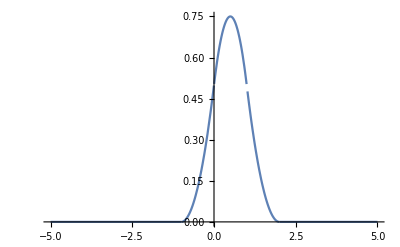

```mathematica
F[x_] = Piecewise[{{1+x,x<0&&x≥-1},{1-x,x≥0 && x<1}},0]
Integrate[F[x]-F[x-1],x]
WaveletFilterCoefficients[BiorthogonalSplineWavelet[3,1],"DualHighpass",WorkingPrecision->∞]
Plot[Piecewise[{{0, x≤-1}, {1/2+x+x^2/2, -1<x≤0}, {1/2+x-x^2, 0<x≤1}, {2-2 x+x^2/2, 1<x≤2}, {0, 2<x}}],{x,-5,5},PlotRange->All]
```

```mathematica
Piecewise[{{0, x≤-1}, {1/2+x+x^2/2, -1<x≤0}, {1/2+x-x^2, 0<x≤1}, {2-2 x+x^2/2, 1<x≤2}, {0, 2<x}}]
```

Piecewise[{{0, x≤-1}, {1/2+x+x^2/2, -1<x≤0}, {1/2+x-x^2, 0<x≤1}, {2-2 x+x^2/2, 1<x≤2}, {0, True}}]